## VFD demo

Load the package.

```mathematica
Needs["VFD`"]
```

Produce a simple plot.

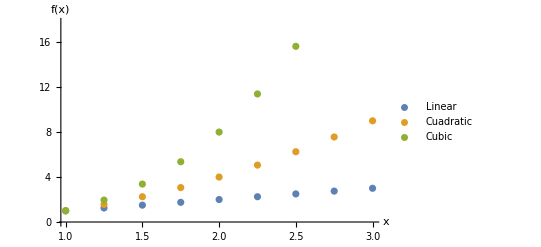

```mathematica
plot=ListPlot[Table[{x,x^k},{k,1,3},{x,1,3,0.25}],PlotLegends->{"Linear","Cuadratic","Cubic"},AxesLabel->{"x","f(x)"}]
```

Produce a VFD with the plot itself.

```mathematica
vfd=PlotToVFD[plot];
```

Open the file with the vfd cli.

```mathematica
PreviewVFD[vfd]
```

Directly export with matplotlib.

```mathematica
ExportVFD["demo.pdf",vfd]
```

demo.pdf